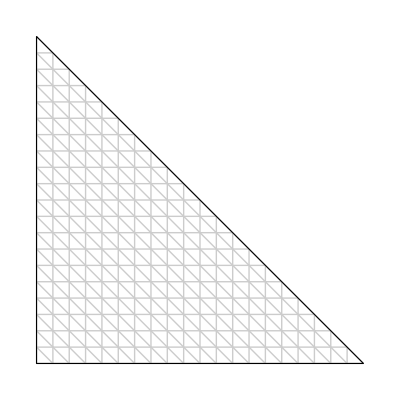

```mathematica
equilateral=Graphics[{
{GrayLevel[0.8],Thin,Table[{
Line[{{i/2,i*√3/2},{1-i/2,i*√3/2}}],
Line[{{i,0},{i/2,i*√3/2}}],
Line[{{1-i,0},{1-i/2,i*√3/2}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]}
},AspectRatio->1,(*Frame->True,*)ImageSize->400];

right=Graphics[{
{Thin,GrayLevel[0.8],Table[{
Line[{{0,i},{1-i,i}}],
Line[{{i,0},{i,1-i}}],
Line[{{0,i},{i,0}}]
},{i,0,1,0.05}]
},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]}
},AspectRatio->1,(*Frame->True,*)ImageSize->400]

(*Grid[{{Show[equilateral],Show[right]}}]*)
```

```mathematica
(*,
Line[{{0,i},{(1-i)/2,i+(1-i)/2}}],
Line[{{i,0},{(1+i)/2,(1+i)/2-i}}]*)
```